```mathematica
(*css zebrafinch model*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs(lsI vI z +lsO qO ) + nh vh(lhI vI z +lhO qO );
NNn :=ns vs(lsI vI (1-z)+lsO(1- qO) ) + nh vh(lhI vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs(lsI vI z +lsO qO ), vh(lhI vI z +lhO qO ), 0, 0}, {vs(lsI vI (1-z)+lsO(1- qO) ), vh(lhI vI (1-z)+lhO(1- qO) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa]/.{lhV -> 0, lsV->0};
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→(-bn lhO u vh+bn lhO pn u vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn u vs-bn lsI pn vI vs+ba lhI vh vI z-bn lhI vh vI z-ba lhI pa vh vI z+bn lhI pn vh vI z+ba lsI pa vI vs z-bn lsI pn vI vs z-√(-4 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs) (-bn lhI vh vI z+bn lhI pn vh vI z-bn lsI pn vI vs z)+(bn lhO u vh-bn lhO pn u vh+bn lhI vh vI-bn lhI pn vh vI+bn lsO pn u vs+bn lsI pn vI vs-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2))/(2 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs))},{Fa→(-bn lhO u vh+bn lhO pn u vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn u vs-bn lsI pn vI vs+ba lhI vh vI z-bn lhI vh vI z-ba lhI pa vh vI z+bn lhI pn vh vI z+ba lsI pa vI vs z-bn lsI pn vI vs z+√(-4 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs) (-bn lhI vh vI z+bn lhI pn vh vI z-bn lsI pn vI vs z)+(bn lhO u vh-bn lhO pn u vh+bn lhI vh vI-bn lhI pn vh vI+bn lsO pn u vs+bn lsI pn vI vs-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2))/(2 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs))}}

```mathematica
subtest = {ba->3,bn->1,z->0.6,pa->0.1,pn->0.9,vs->0.8,vh->0.95,vI->0.7  ,lsO-> 0.2 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2 ,u-> 0.1 };
```

```mathematica
Fasols[[2,1,2]]/.subtest (*check it is stable qhat*)
 Fasols[[2,1,2]]
```

0.480835

(-bn lhO u vh+bn lhO pn u vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn u vs-bn lsI pn vI vs+ba lhI vh vI z-bn lhI vh vI z-ba lhI pa vh vI z+bn lhI pn vh vI z+ba lsI pa vI vs z-bn lsI pn vI vs z+√(-4 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs) (-bn lhI vh vI z+bn lhI pn vh vI z-bn lsI pn vI vs z)+(bn lhO u vh-bn lhO pn u vh+bn lhI vh vI-bn lhI pn vh vI+bn lsO pn u vs+bn lsI pn vI vs-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2))/(2 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs))

```mathematica
Qhat := (-bn lhO u vh+bn lhO pn u vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn u vs-bn lsI pn vI vs+ba lhI vh vI z-bn lhI vh vI z-ba lhI pa vh vI z+bn lhI pn vh vI z+ba lsI pa vI vs z-bn lsI pn vI vs z+√(-4 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs) (-bn lhI vh vI z+bn lhI pn vh vI z-bn lsI pn vI vs z)+(bn lhO u vh-bn lhO pn u vh+bn lhI vh vI-bn lhI pn vh vI+bn lsO pn u vs+bn lsI pn vI vs-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2))/(2 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs));
```

```mathematica
AA2=AA/.{Na->Qh,Nn->(1-Qh)};
```

```mathematica
AA3=AA2/.{Qh->Qhat};
```

```mathematica
AA4=AA3/.{pa->0,pn->1}
```

{{0,0,0,bn},{0,0,ba,0},{vs (lsI vI z+(lsO (1-u) (-bn lsO u vs-bn lsI vI vs+ba lhI vh vI z-bn lsI vI vs z+√(4 bn lsI vI vs (ba lhO u vh+ba lhI vh vI-bn lsO u vs-bn lsI vI vs) z+(bn lsO u vs+bn lsI vI vs-ba lhI vh vI z+bn lsI vI vs z)^2)))/(2 (ba lhO u vh+ba lhI vh vI-bn lsO u vs-bn lsI vI vs))),vh (lhI vI z+(lhO (1-u) (-bn lsO u vs-bn lsI vI vs+ba lhI vh vI z-bn lsI vI vs z+√(4 bn lsI vI vs (ba lhO u vh+ba lhI vh vI-bn lsO u vs-bn lsI vI vs) z+(bn lsO u vs+bn lsI vI vs-ba lhI vh vI z+bn lsI vI vs z)^2)))/(2 (ba lhO u vh+ba lhI vh vI-bn lsO u vs-bn lsI vI vs))),0,0},{vs (lsI vI (1-z)+lsO (1-((1-u) (-bn lsO u vs-bn lsI vI vs+ba lhI vh vI z-bn lsI vI vs z+√(4 bn lsI vI vs (ba lhO u vh+ba lhI vh vI-bn lsO u vs-bn lsI vI vs) z+(bn lsO u vs+bn lsI vI vs-ba lhI vh vI z+bn lsI vI vs z)^2)))/(2 (ba lhO u vh+ba lhI vh vI-bn lsO u vs-bn lsI vI vs)))),vh (lhI vI (1-z)+lhO (1-((1-u) (-bn lsO u vs-bn lsI vI vs+ba lhI vh vI z-bn lsI vI vs z+√(4 bn lsI vI vs (ba lhO u vh+ba lhI vh vI-bn lsO u vs-bn lsI vI vs) z+(bn lsO u vs+bn lsI vI vs-ba lhI vh vI z+bn lsI vI vs z)^2)))/(2 (ba lhO u vh+ba lhI vh vI-bn lsO u vs-bn lsI vI vs)))),0,0}}

```mathematica
LL=Eigenvalues[AA4]
```

{-(√(2 ba^2 bn lhO^2 lsO u^2 vh^2 vs+104))/(2 √2 (-ba lhO u vh-ba lhI vh vI+bn lsO u vs+bn lsI vI vs)),(√(2 ba^2 bn lhO^2 lsO u^2 vh^2 vs+104))/(2 √2 (-ba lhO u vh-ba lhI vh vI+bn lsO u vs+bn lsI vI vs)),-(√(2 ba^2 bn lhO^2 lsO u^2 vh^2 vs+102+√((1)^2-4 (-8 ba^4 bn^2 lhO^4 lsI lsO u^4 vh^4 vI vs^2+397))))/(2 √2 (-ba lhO u vh-ba lhI vh vI+bn lsO u vs+bn lsI vI vs)),(√(2 ba^2 bn lhO^2 lsO u^2 vh^2 vs+102+√((105+2 bn^2 lsI lsO u vI vs^2 √(4 bn lsI vI vs (ba lhO u vh+5) z+1^2))^2-4 (-8 ba^4 bn^2 lhO^4 lsI lsO u^4 vh^4 vI vs^2+397))))/(2 √2 (-ba lhO u vh-ba lhI vh vI+bn lsO u vs+bn lsI vI vs))}
 |  |  |  |

```mathematica
LL/.subtest
```

{0.+0.325938 ⅈ,0.-0.325938 ⅈ,1.25866,-1.25866}

```mathematica
Simplify[LL[[3]]]
```

1/(2 ba vh (lhO u+lhI vI)-2 bn (lsO u+lsI vI) vs)(√(ba^2 bn lhO^2 lsO u^2 vh^2 vs+ba^2 bn lhO^2 lsO u^3 vh^2 vs-ba^2 bn lhO^2 lsI u vh^2 vI vs+3 ba^2 bn lhI lhO lsO u vh^2 vI vs+3 ba^2 bn lhO^2 lsI u^2 vh^2 vI vs+ba^2 bn lhI lhO lsO u^2 vh^2 vI vs-ba^2 bn lhI lhO lsI vh^2 vI^2 vs+2 ba^2 bn lhI^2 lsO vh^2 vI^2 vs+5 ba^2 bn lhI lhO lsI u vh^2 vI^2 vs+2 ba^2 bn lhI^2 lsI vh^2 vI^3 vs-2 ba bn^2 lhO lsO^2 u^2 vh vs^2-2 ba bn^2 lhO lsO^2 u^3 vh vs^2-ba bn^2 lhO lsI lsO u vh vI vs^2-3 ba bn^2 lhI lsO^2 u vh vI vs^2-7 ba bn^2 lhO lsI lsO u^2 vh vI vs^2-ba bn^2 lhI lsO^2 u^2 vh vI vs^2+ba bn^2 lhO lsI^2 vh vI^2 vs^2-3 ba bn^2 lhI lsI lsO vh vI^2 vs^2-5 ba bn^2 lhO lsI^2 u vh vI^2 vs^2-5 ba bn^2 lhI lsI lsO u vh vI^2 vs^2-4 ba bn^2 lhI lsI^2 vh vI^3 vs^2+bn^3 lsO^3 u^2 vs^3+bn^3 lsO^3 u^3 vs^3+2 bn^3 lsI lsO^2 u vI vs^3+4 bn^3 lsI lsO^2 u^2 vI vs^3+bn^3 lsI^2 lsO vI^2 vs^3+5 bn^3 lsI^2 lsO u vI^2 vs^3+2 bn^3 lsI^3 vI^3 vs^3+ba^3 lhI lhO^2 u vh^3 vI z+ba^3 lhI lhO^2 u^2 vh^3 vI z+ba^3 lhI^2 lhO vh^3 vI^2 z+3 ba^3 lhI^2 lhO u vh^3 vI^2 z+2 ba^3 lhI^3 vh^3 vI^3 z-ba^2 bn lhO^2 lsI u vh^2 vI vs z-2 ba^2 bn lhI lhO lsO u vh^2 vI vs z-ba^2 bn lhO^2 lsI u^2 vh^2 vI vs z-2 ba^2 bn lhI lhO lsO u^2 vh^2 vI vs z-2 ba^2 bn lhI lhO lsI vh^2 vI^2 vs z-ba^2 bn lhI^2 lsO vh^2 vI^2 vs z-6 ba^2 bn lhI lhO lsI u vh^2 vI^2 vs z-3 ba^2 bn lhI^2 lsO u vh^2 vI^2 vs z-6 ba^2 bn lhI^2 lsI vh^2 vI^3 vs z+2 ba bn^2 lhO lsI lsO u vh vI vs^2 z+ba bn^2 lhI lsO^2 u vh vI vs^2 z+2 ba bn^2 lhO lsI lsO u^2 vh vI vs^2 z+ba bn^2 lhI lsO^2 u^2 vh vI vs^2 z+ba bn^2 lhO lsI^2 vh vI^2 vs^2 z+2 ba bn^2 lhI lsI lsO vh vI^2 vs^2 z+3 ba bn^2 lhO lsI^2 u vh vI^2 vs^2 z+6 ba bn^2 lhI lsI lsO u vh vI^2 vs^2 z+6 ba bn^2 lhI lsI^2 vh vI^3 vs^2 z-bn^3 lsI lsO^2 u vI vs^3 z-bn^3 lsI lsO^2 u^2 vI vs^3 z-bn^3 lsI^2 lsO vI^2 vs^3 z-3 bn^3 lsI^2 lsO u vI^2 vs^3 z-2 bn^3 lsI^3 vI^3 vs^3 z+ba^2 lhO^2 u vh^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba^2 lhO^2 u^2 vh^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba^2 lhI lhO vh^2 vI √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba^2 lhI lhO u vh^2 vI √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-2 ba bn lhO lsO u vh vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+2 ba bn lhO lsO u^2 vh vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba bn lhO lsI vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba bn lhI lsO vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba bn lhO lsI u vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba bn lhI lsO u vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+bn^2 lsO^2 u vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-bn^2 lsO^2 u^2 vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+bn^2 lsI lsO vI vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-bn^2 lsI lsO u vI vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+√2 √((ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs)^2 (ba^4 lhI^2 vh^4 vI^2 (lhO^2 (1+u^2)+2 lhI lhO (1+u) vI+2 lhI^2 vI^2) z^2+bn^3 vs^3 (lsO u-lsI vI (-1+z)) (bn (lsO^2 (1+u^2)+2 lsI lsO (1+u) vI+2 lsI^2 vI^2) vs (lsO u-lsI vI (-1+z))-lsO (-1+u) (lsO+lsO u+2 lsI vI) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2))-ba^3 vh^3 vI z (lhI lhO (-1+u) (lhO+lhO u+2 lhI vI) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2)+2 bn vs (-lhO^3 lsI u (1+u)^2+lhI lhO^2 (2 lsO u^2+lsI vI (-6 u+u^2 (-4+z)+z))+lhI^2 lhO vI (lsI vI (-2+3 u (-2+z)+3 z)+lsO (-1+4 u+z+u^2 (1+z)))+lhI^3 vI^2 (2 lsI vI (-1+2 z)+lsO (z+u (2+z)))))+ba^2 bn vh^2 vs (-(-1+u) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2) (-2 lhI^2 lsO vI^2 (-2+z)+lhO^2 (1+u) (lsO u-lsI vI (1+z))-2 lhI lhO vI (lsO (-1+u (-2+z)+z)+lsI vI (1+2 z)))+bn vs (lhO^2 (lsO^2 (u^2+u^4)-2 lsI lsO u vI (3 z+3 u^2 z+u (-2+4 z))+lsI^2 vI^2 (1-12 u z+z^2+u^2 (1-8 z+z^2)))+2 lhI lhO vI (lsI^2 vI^2 (1+u-4 z-12 u z+3 z^2+3 u z^2)+lsO^2 u (1+2 u^2+u (-1+4 z))+lsI lsO vI (-1-4 u (-1+z)-2 z+2 z^2+u^2 (1-6 z+2 z^2)))+lhI^2 vI^2 (2 lsI^2 vI^2 (1-6 z+6 z^2)+lsO^2 (2-2 z+z^2+u (-4+8 z)+u^2 (4+2 z+z^2))+2 lsI lsO vI (z (-2+3 z)+u (2+3 z^2)))))-ba bn^2 vh vs^2 (-(-1+u) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2) (2 lhO (lsO^2 u (1+u)-lsI^2 vI^2 (1+z)-lsI lsO vI (u (-1+z)+z))-lhI lsO vI (lsO (-2+u (-4+z)+z)+2 lsI vI (-3+2 z)))+2 bn vs (lhO (lsO^3 (u^2+u^4)+lsI lsO^2 u vI (1+u^2 (2-3 z)+u (3-2 z)-3 z)+lsI^2 lsO vI^2 (u (4-8 z)+(-1+z) z+u^2 (2-7 z+z^2))+lsI^3 vI^3 ((-1+z)^2+u (1-6 z+z^2)))+lhI vI (2 lsI^3 vI^3 (1-3 z+2 z^2)+lsO^3 u (1+2 u^2+u (-1+2 z))+lsI lsO^2 vI ((-1+z)^2+2 u z+u^2 (5-2 z+z^2))+lsI^2 lsO vI^2 (1-4 z+3 z^2+u (5-6 z+3 z^2)))))))))

```mathematica
Lambda1[lsI_, lhI_, lsO_, lhO_]:= 1/(2 ba vh (lhO u+lhI vI)-2 bn (lsO u+lsI vI) vs)(√(ba^2 bn lhO^2 lsO u^2 vh^2 vs+ba^2 bn lhO^2 lsO u^3 vh^2 vs-ba^2 bn lhO^2 lsI u vh^2 vI vs+3 ba^2 bn lhI lhO lsO u vh^2 vI vs+3 ba^2 bn lhO^2 lsI u^2 vh^2 vI vs+ba^2 bn lhI lhO lsO u^2 vh^2 vI vs-ba^2 bn lhI lhO lsI vh^2 vI^2 vs+2 ba^2 bn lhI^2 lsO vh^2 vI^2 vs+5 ba^2 bn lhI lhO lsI u vh^2 vI^2 vs+2 ba^2 bn lhI^2 lsI vh^2 vI^3 vs-2 ba bn^2 lhO lsO^2 u^2 vh vs^2-2 ba bn^2 lhO lsO^2 u^3 vh vs^2-ba bn^2 lhO lsI lsO u vh vI vs^2-3 ba bn^2 lhI lsO^2 u vh vI vs^2-7 ba bn^2 lhO lsI lsO u^2 vh vI vs^2-ba bn^2 lhI lsO^2 u^2 vh vI vs^2+ba bn^2 lhO lsI^2 vh vI^2 vs^2-3 ba bn^2 lhI lsI lsO vh vI^2 vs^2-5 ba bn^2 lhO lsI^2 u vh vI^2 vs^2-5 ba bn^2 lhI lsI lsO u vh vI^2 vs^2-4 ba bn^2 lhI lsI^2 vh vI^3 vs^2+bn^3 lsO^3 u^2 vs^3+bn^3 lsO^3 u^3 vs^3+2 bn^3 lsI lsO^2 u vI vs^3+4 bn^3 lsI lsO^2 u^2 vI vs^3+bn^3 lsI^2 lsO vI^2 vs^3+5 bn^3 lsI^2 lsO u vI^2 vs^3+2 bn^3 lsI^3 vI^3 vs^3+ba^3 lhI lhO^2 u vh^3 vI z+ba^3 lhI lhO^2 u^2 vh^3 vI z+ba^3 lhI^2 lhO vh^3 vI^2 z+3 ba^3 lhI^2 lhO u vh^3 vI^2 z+2 ba^3 lhI^3 vh^3 vI^3 z-ba^2 bn lhO^2 lsI u vh^2 vI vs z-2 ba^2 bn lhI lhO lsO u vh^2 vI vs z-ba^2 bn lhO^2 lsI u^2 vh^2 vI vs z-2 ba^2 bn lhI lhO lsO u^2 vh^2 vI vs z-2 ba^2 bn lhI lhO lsI vh^2 vI^2 vs z-ba^2 bn lhI^2 lsO vh^2 vI^2 vs z-6 ba^2 bn lhI lhO lsI u vh^2 vI^2 vs z-3 ba^2 bn lhI^2 lsO u vh^2 vI^2 vs z-6 ba^2 bn lhI^2 lsI vh^2 vI^3 vs z+2 ba bn^2 lhO lsI lsO u vh vI vs^2 z+ba bn^2 lhI lsO^2 u vh vI vs^2 z+2 ba bn^2 lhO lsI lsO u^2 vh vI vs^2 z+ba bn^2 lhI lsO^2 u^2 vh vI vs^2 z+ba bn^2 lhO lsI^2 vh vI^2 vs^2 z+2 ba bn^2 lhI lsI lsO vh vI^2 vs^2 z+3 ba bn^2 lhO lsI^2 u vh vI^2 vs^2 z+6 ba bn^2 lhI lsI lsO u vh vI^2 vs^2 z+6 ba bn^2 lhI lsI^2 vh vI^3 vs^2 z-bn^3 lsI lsO^2 u vI vs^3 z-bn^3 lsI lsO^2 u^2 vI vs^3 z-bn^3 lsI^2 lsO vI^2 vs^3 z-3 bn^3 lsI^2 lsO u vI^2 vs^3 z-2 bn^3 lsI^3 vI^3 vs^3 z+ba^2 lhO^2 u vh^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba^2 lhO^2 u^2 vh^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba^2 lhI lhO vh^2 vI √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba^2 lhI lhO u vh^2 vI √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-2 ba bn lhO lsO u vh vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+2 ba bn lhO lsO u^2 vh vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba bn lhO lsI vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba bn lhI lsO vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba bn lhO lsI u vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba bn lhI lsO u vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+bn^2 lsO^2 u vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-bn^2 lsO^2 u^2 vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+bn^2 lsI lsO vI vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-bn^2 lsI lsO u vI vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+√2 √((ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs)^2 (ba^4 lhI^2 vh^4 vI^2 (lhO^2 (1+u^2)+2 lhI lhO (1+u) vI+2 lhI^2 vI^2) z^2+bn^3 vs^3 (lsO u-lsI vI (-1+z)) (bn (lsO^2 (1+u^2)+2 lsI lsO (1+u) vI+2 lsI^2 vI^2) vs (lsO u-lsI vI (-1+z))-lsO (-1+u) (lsO+lsO u+2 lsI vI) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2))-ba^3 vh^3 vI z (lhI lhO (-1+u) (lhO+lhO u+2 lhI vI) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2)+2 bn vs (-lhO^3 lsI u (1+u)^2+lhI lhO^2 (2 lsO u^2+lsI vI (-6 u+u^2 (-4+z)+z))+lhI^2 lhO vI (lsI vI (-2+3 u (-2+z)+3 z)+lsO (-1+4 u+z+u^2 (1+z)))+lhI^3 vI^2 (2 lsI vI (-1+2 z)+lsO (z+u (2+z)))))+ba^2 bn vh^2 vs (-(-1+u) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2) (-2 lhI^2 lsO vI^2 (-2+z)+lhO^2 (1+u) (lsO u-lsI vI (1+z))-2 lhI lhO vI (lsO (-1+u (-2+z)+z)+lsI vI (1+2 z)))+bn vs (lhO^2 (lsO^2 (u^2+u^4)-2 lsI lsO u vI (3 z+3 u^2 z+u (-2+4 z))+lsI^2 vI^2 (1-12 u z+z^2+u^2 (1-8 z+z^2)))+2 lhI lhO vI (lsI^2 vI^2 (1+u-4 z-12 u z+3 z^2+3 u z^2)+lsO^2 u (1+2 u^2+u (-1+4 z))+lsI lsO vI (-1-4 u (-1+z)-2 z+2 z^2+u^2 (1-6 z+2 z^2)))+lhI^2 vI^2 (2 lsI^2 vI^2 (1-6 z+6 z^2)+lsO^2 (2-2 z+z^2+u (-4+8 z)+u^2 (4+2 z+z^2))+2 lsI lsO vI (z (-2+3 z)+u (2+3 z^2)))))-ba bn^2 vh vs^2 (-(-1+u) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2) (2 lhO (lsO^2 u (1+u)-lsI^2 vI^2 (1+z)-lsI lsO vI (u (-1+z)+z))-lhI lsO vI (lsO (-2+u (-4+z)+z)+2 lsI vI (-3+2 z)))+2 bn vs (lhO (lsO^3 (u^2+u^4)+lsI lsO^2 u vI (1+u^2 (2-3 z)+u (3-2 z)-3 z)+lsI^2 lsO vI^2 (u (4-8 z)+(-1+z) z+u^2 (2-7 z+z^2))+lsI^3 vI^3 ((-1+z)^2+u (1-6 z+z^2)))+lhI vI (2 lsI^3 vI^3 (1-3 z+2 z^2)+lsO^3 u (1+2 u^2+u (-1+2 z))+lsI lsO^2 vI ((-1+z)^2+2 u z+u^2 (5-2 z+z^2))+lsI^2 lsO vI^2 (1-4 z+3 z^2+u (5-6 z+3 z^2)))))))));
```

```mathematica
DlsI=D[Lambda1[lsI, lhI, lsO, lhO],lsI];
```

```mathematica
DlhI=D[Lambda1[lsI, lhI, lsO, lhO],lhI];
```

```mathematica
DlsO=D[Lambda1[lsI, lhI, lsO, lhO],lsO];
```

```mathematica
DlhO=D[Lambda1[lsI, lhI, lsO, lhO],lhO];
```

```mathematica
(*try and graph*)
lsIstart=0.5;
lhIstart=0.5;
lsOstart=0.5;
lhOstart=0.5;
imax=300;
lsItab=lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsItab=Table[0,{i,imax}];
DlhItab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.01;
sub2={ba->2,bn->1,z->0.8,vs->0.6,vh->0.9,vI->0.7  ,u->0.15};
lsItab[[1]]=lsIstart;
lsOtab[[1]]=lsOstart;
lhItab[[1]]=lhIstart;
lhOtab[[1]]=lhOstart;
DlsItab[[1]]=DlsI/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlhItab[[1]]=DlhI/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlsOtab[[1]]=DlsO/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
```

```mathematica
For[i=2,i<imax,i++,{
lsItab[[i]]=lsItab[[i-1]]+ delta DlsI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsItab[[i]]=If[lsItab[[i]]>1,1,lsItab[[i]]];
lsItab[[i]]=If[lsItab[[i]]<0,0,lsItab[[i]]];

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhItab[[i]]=lhItab[[i-1]] + delta DlhI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhItab[[i]]=If[lhItab[[i]]>1,1,lhItab[[i]]];
lhItab[[i]]=If[lhItab[[i]]<0,0,lhItab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsItab[[i]]=DlsI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhItab[[i]]=DlhI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlsOtab[[i]]=DlsO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

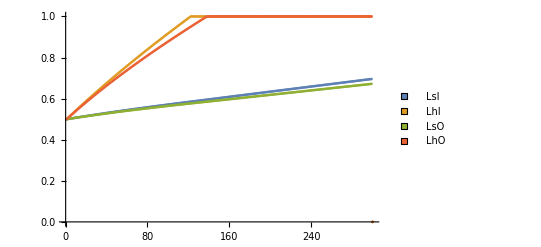

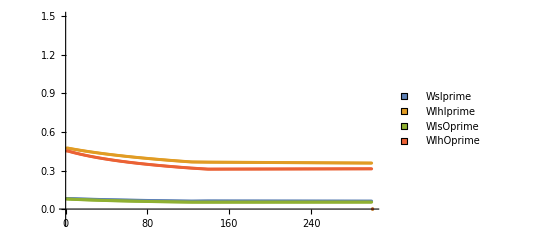

```mathematica
ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsI,LhI,LsO,LhO},LegendMarkers->Graphics[Rectangle[]]]] 
ListPlot[{DlsItab,DlhItab,DlsOtab,DlhOtab},PlotRange->{All,{-.1,1.5}},PlotLegends->PointLegend[{WsIprime,WlhIprime,WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]]]
```

```mathematica
(*try with 2 derivatives*)
Lambda2= 1/(2 ba vh (lhO u+lhI vI)-2 bn (lsO u+lsI vI) vs)(√(ba^2 bn lhO^2 lsO u^2 vh^2 vs+ba^2 bn lhO^2 lsO u^3 vh^2 vs-ba^2 bn lhO^2 lsI u vh^2 vI vs+3 ba^2 bn lhI lhO lsO u vh^2 vI vs+3 ba^2 bn lhO^2 lsI u^2 vh^2 vI vs+ba^2 bn lhI lhO lsO u^2 vh^2 vI vs-ba^2 bn lhI lhO lsI vh^2 vI^2 vs+2 ba^2 bn lhI^2 lsO vh^2 vI^2 vs+5 ba^2 bn lhI lhO lsI u vh^2 vI^2 vs+2 ba^2 bn lhI^2 lsI vh^2 vI^3 vs-2 ba bn^2 lhO lsO^2 u^2 vh vs^2-2 ba bn^2 lhO lsO^2 u^3 vh vs^2-ba bn^2 lhO lsI lsO u vh vI vs^2-3 ba bn^2 lhI lsO^2 u vh vI vs^2-7 ba bn^2 lhO lsI lsO u^2 vh vI vs^2-ba bn^2 lhI lsO^2 u^2 vh vI vs^2+ba bn^2 lhO lsI^2 vh vI^2 vs^2-3 ba bn^2 lhI lsI lsO vh vI^2 vs^2-5 ba bn^2 lhO lsI^2 u vh vI^2 vs^2-5 ba bn^2 lhI lsI lsO u vh vI^2 vs^2-4 ba bn^2 lhI lsI^2 vh vI^3 vs^2+bn^3 lsO^3 u^2 vs^3+bn^3 lsO^3 u^3 vs^3+2 bn^3 lsI lsO^2 u vI vs^3+4 bn^3 lsI lsO^2 u^2 vI vs^3+bn^3 lsI^2 lsO vI^2 vs^3+5 bn^3 lsI^2 lsO u vI^2 vs^3+2 bn^3 lsI^3 vI^3 vs^3+ba^3 lhI lhO^2 u vh^3 vI z+ba^3 lhI lhO^2 u^2 vh^3 vI z+ba^3 lhI^2 lhO vh^3 vI^2 z+3 ba^3 lhI^2 lhO u vh^3 vI^2 z+2 ba^3 lhI^3 vh^3 vI^3 z-ba^2 bn lhO^2 lsI u vh^2 vI vs z-2 ba^2 bn lhI lhO lsO u vh^2 vI vs z-ba^2 bn lhO^2 lsI u^2 vh^2 vI vs z-2 ba^2 bn lhI lhO lsO u^2 vh^2 vI vs z-2 ba^2 bn lhI lhO lsI vh^2 vI^2 vs z-ba^2 bn lhI^2 lsO vh^2 vI^2 vs z-6 ba^2 bn lhI lhO lsI u vh^2 vI^2 vs z-3 ba^2 bn lhI^2 lsO u vh^2 vI^2 vs z-6 ba^2 bn lhI^2 lsI vh^2 vI^3 vs z+2 ba bn^2 lhO lsI lsO u vh vI vs^2 z+ba bn^2 lhI lsO^2 u vh vI vs^2 z+2 ba bn^2 lhO lsI lsO u^2 vh vI vs^2 z+ba bn^2 lhI lsO^2 u^2 vh vI vs^2 z+ba bn^2 lhO lsI^2 vh vI^2 vs^2 z+2 ba bn^2 lhI lsI lsO vh vI^2 vs^2 z+3 ba bn^2 lhO lsI^2 u vh vI^2 vs^2 z+6 ba bn^2 lhI lsI lsO u vh vI^2 vs^2 z+6 ba bn^2 lhI lsI^2 vh vI^3 vs^2 z-bn^3 lsI lsO^2 u vI vs^3 z-bn^3 lsI lsO^2 u^2 vI vs^3 z-bn^3 lsI^2 lsO vI^2 vs^3 z-3 bn^3 lsI^2 lsO u vI^2 vs^3 z-2 bn^3 lsI^3 vI^3 vs^3 z+ba^2 lhO^2 u vh^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba^2 lhO^2 u^2 vh^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba^2 lhI lhO vh^2 vI √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba^2 lhI lhO u vh^2 vI √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-2 ba bn lhO lsO u vh vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+2 ba bn lhO lsO u^2 vh vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba bn lhO lsI vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-ba bn lhI lsO vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba bn lhO lsI u vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+ba bn lhI lsO u vh vI vs √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+bn^2 lsO^2 u vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-bn^2 lsO^2 u^2 vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+bn^2 lsI lsO vI vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)-bn^2 lsI lsO u vI vs^2 √(4 bn lsI vI vs (ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs) z+(ba lhI vh vI z-bn vs (lsO u+lsI vI (1+z)))^2)+√2 √((ba vh (lhO u+lhI vI)-bn (lsO u+lsI vI) vs)^2 (ba^4 lhI^2 vh^4 vI^2 (lhO^2 (1+u^2)+2 lhI lhO (1+u) vI+2 lhI^2 vI^2) z^2+bn^3 vs^3 (lsO u-lsI vI (-1+z)) (bn (lsO^2 (1+u^2)+2 lsI lsO (1+u) vI+2 lsI^2 vI^2) vs (lsO u-lsI vI (-1+z))-lsO (-1+u) (lsO+lsO u+2 lsI vI) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2))-ba^3 vh^3 vI z (lhI lhO (-1+u) (lhO+lhO u+2 lhI vI) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2)+2 bn vs (-lhO^3 lsI u (1+u)^2+lhI lhO^2 (2 lsO u^2+lsI vI (-6 u+u^2 (-4+z)+z))+lhI^2 lhO vI (lsI vI (-2+3 u (-2+z)+3 z)+lsO (-1+4 u+z+u^2 (1+z)))+lhI^3 vI^2 (2 lsI vI (-1+2 z)+lsO (z+u (2+z)))))+ba^2 bn vh^2 vs (-(-1+u) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2) (-2 lhI^2 lsO vI^2 (-2+z)+lhO^2 (1+u) (lsO u-lsI vI (1+z))-2 lhI lhO vI (lsO (-1+u (-2+z)+z)+lsI vI (1+2 z)))+bn vs (lhO^2 (lsO^2 (u^2+u^4)-2 lsI lsO u vI (3 z+3 u^2 z+u (-2+4 z))+lsI^2 vI^2 (1-12 u z+z^2+u^2 (1-8 z+z^2)))+2 lhI lhO vI (lsI^2 vI^2 (1+u-4 z-12 u z+3 z^2+3 u z^2)+lsO^2 u (1+2 u^2+u (-1+4 z))+lsI lsO vI (-1-4 u (-1+z)-2 z+2 z^2+u^2 (1-6 z+2 z^2)))+lhI^2 vI^2 (2 lsI^2 vI^2 (1-6 z+6 z^2)+lsO^2 (2-2 z+z^2+u (-4+8 z)+u^2 (4+2 z+z^2))+2 lsI lsO vI (z (-2+3 z)+u (2+3 z^2)))))-ba bn^2 vh vs^2 (-(-1+u) √(bn^2 vs^2 (lsO u-lsI vI (-1+z))^2-2 ba bn vh vI vs (-2 lhO lsI u+lhI lsO u+lhI lsI vI (-1+z)) z+ba^2 lhI^2 vh^2 vI^2 z^2) (2 lhO (lsO^2 u (1+u)-lsI^2 vI^2 (1+z)-lsI lsO vI (u (-1+z)+z))-lhI lsO vI (lsO (-2+u (-4+z)+z)+2 lsI vI (-3+2 z)))+2 bn vs (lhO (lsO^3 (u^2+u^4)+lsI lsO^2 u vI (1+u^2 (2-3 z)+u (3-2 z)-3 z)+lsI^2 lsO vI^2 (u (4-8 z)+(-1+z) z+u^2 (2-7 z+z^2))+lsI^3 vI^3 ((-1+z)^2+u (1-6 z+z^2)))+lhI vI (2 lsI^3 vI^3 (1-3 z+2 z^2)+lsO^3 u (1+2 u^2+u (-1+2 z))+lsI lsO^2 vI ((-1+z)^2+2 u z+u^2 (5-2 z+z^2))+lsI^2 lsO vI^2 (1-4 z+3 z^2+u (5-6 z+3 z^2)))))))));
Lambda2 = Lambda2/.{lsI-> 1-lsO,lhI-> 1-lhO};
```

```mathematica
Lambda3[lhO_,lsO_] :=1/(2 ba vh (lhO (u-vI)+vI)-2 bn (lsO (u-vI)+vI) vs)(√(ba^2 bn lhO^2 lsO u^2 vh^2 vs+ba^2 bn lhO^2 lsO u^3 vh^2 vs+ba^2 bn lhO^2 (-1+lsO) u vh^2 vI vs-3 ba^2 bn (-1+lhO) lhO lsO u vh^2 vI vs-3 ba^2 bn lhO^2 (-1+lsO) u^2 vh^2 vI vs-ba^2 bn (-1+lhO) lhO lsO u^2 vh^2 vI vs-ba^2 bn (-1+lhO) lhO (-1+lsO) vh^2 vI^2 vs+2 ba^2 bn (-1+lhO)^2 lsO vh^2 vI^2 vs+5 ba^2 bn (-1+lhO) lhO (-1+lsO) u vh^2 vI^2 vs-2 ba^2 bn (-1+lhO)^2 (-1+lsO) vh^2 vI^3 vs-2 ba bn^2 lhO lsO^2 u^2 vh vs^2-2 ba bn^2 lhO lsO^2 u^3 vh vs^2+ba bn^2 lhO (-1+lsO) lsO u vh vI vs^2+3 ba bn^2 (-1+lhO) lsO^2 u vh vI vs^2+7 ba bn^2 lhO (-1+lsO) lsO u^2 vh vI vs^2+ba bn^2 (-1+lhO) lsO^2 u^2 vh vI vs^2+ba bn^2 lhO (-1+lsO)^2 vh vI^2 vs^2-3 ba bn^2 (-1+lhO) (-1+lsO) lsO vh vI^2 vs^2-5 ba bn^2 lhO (-1+lsO)^2 u vh vI^2 vs^2-5 ba bn^2 (-1+lhO) (-1+lsO) lsO u vh vI^2 vs^2+4 ba bn^2 (-1+lhO) (-1+lsO)^2 vh vI^3 vs^2+bn^3 lsO^3 u^2 vs^3+bn^3 lsO^3 u^3 vs^3-2 bn^3 (-1+lsO) lsO^2 u vI vs^3-4 bn^3 (-1+lsO) lsO^2 u^2 vI vs^3+bn^3 (-1+lsO)^2 lsO vI^2 vs^3+5 bn^3 (-1+lsO)^2 lsO u vI^2 vs^3-2 bn^3 (-1+lsO)^3 vI^3 vs^3-ba^3 (-1+lhO) lhO^2 u vh^3 vI z-ba^3 (-1+lhO) lhO^2 u^2 vh^3 vI z+ba^3 (-1+lhO)^2 lhO vh^3 vI^2 z+3 ba^3 (-1+lhO)^2 lhO u vh^3 vI^2 z-2 ba^3 (-1+lhO)^3 vh^3 vI^3 z+ba^2 bn lhO^2 (-1+lsO) u vh^2 vI vs z+2 ba^2 bn (-1+lhO) lhO lsO u vh^2 vI vs z+ba^2 bn lhO^2 (-1+lsO) u^2 vh^2 vI vs z+2 ba^2 bn (-1+lhO) lhO lsO u^2 vh^2 vI vs z-2 ba^2 bn (-1+lhO) lhO (-1+lsO) vh^2 vI^2 vs z-ba^2 bn (-1+lhO)^2 lsO vh^2 vI^2 vs z-6 ba^2 bn (-1+lhO) lhO (-1+lsO) u vh^2 vI^2 vs z-3 ba^2 bn (-1+lhO)^2 lsO u vh^2 vI^2 vs z+6 ba^2 bn (-1+lhO)^2 (-1+lsO) vh^2 vI^3 vs z-2 ba bn^2 lhO (-1+lsO) lsO u vh vI vs^2 z-ba bn^2 (-1+lhO) lsO^2 u vh vI vs^2 z-2 ba bn^2 lhO (-1+lsO) lsO u^2 vh vI vs^2 z-ba bn^2 (-1+lhO) lsO^2 u^2 vh vI vs^2 z+ba bn^2 lhO (-1+lsO)^2 vh vI^2 vs^2 z+2 ba bn^2 (-1+lhO) (-1+lsO) lsO vh vI^2 vs^2 z+3 ba bn^2 lhO (-1+lsO)^2 u vh vI^2 vs^2 z+6 ba bn^2 (-1+lhO) (-1+lsO) lsO u vh vI^2 vs^2 z-6 ba bn^2 (-1+lhO) (-1+lsO)^2 vh vI^3 vs^2 z+bn^3 (-1+lsO) lsO^2 u vI vs^3 z+bn^3 (-1+lsO) lsO^2 u^2 vI vs^3 z-bn^3 (-1+lsO)^2 lsO vI^2 vs^3 z-3 bn^3 (-1+lsO)^2 lsO u vI^2 vs^3 z+2 bn^3 (-1+lsO)^3 vI^3 vs^3 z+ba^2 lhO^2 u vh^2 √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)-ba^2 lhO^2 u^2 vh^2 √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)-ba^2 (-1+lhO) lhO vh^2 vI √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)+ba^2 (-1+lhO) lhO u vh^2 vI √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)-2 ba bn lhO lsO u vh vs √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)+2 ba bn lhO lsO u^2 vh vs √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)+ba bn lhO (-1+lsO) vh vI vs √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)+ba bn (-1+lhO) lsO vh vI vs √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)-ba bn lhO (-1+lsO) u vh vI vs √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)-ba bn (-1+lhO) lsO u vh vI vs √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)+bn^2 lsO^2 u vs^2 √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)-bn^2 lsO^2 u^2 vs^2 √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)-bn^2 (-1+lsO) lsO vI vs^2 √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)+bn^2 (-1+lsO) lsO u vI vs^2 √(4 bn (1-lsO) vI vs (ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs) z+(bn lsO u vs+ba (-1+lhO) vh vI z-bn (-1+lsO) vI vs (1+z))^2)+√2 √((ba vh (lhO (u-vI)+vI)-bn (lsO (u-vI)+vI) vs)^2 (ba^4 (-1+lhO)^2 vh^4 vI^2 (lhO^2 (1+u^2)-2 (-1+lhO) lhO (1+u) vI+2 (-1+lhO)^2 vI^2) z^2+bn^3 vs^3 (lsO u+(-1+lsO) vI (-1+z)) (bn (lsO^2 (1+u^2)-2 (-1+lsO) lsO (1+u) vI+2 (-1+lsO)^2 vI^2) vs (lsO u+(-1+lsO) vI (-1+z))-lsO (-1+u) (lsO (1+u-2 vI)+2 vI) √(bn^2 vs^2 (lsO u+(-1+lsO) vI (-1+z))^2-2 ba bn vh vI vs (2 lhO (-1+lsO) u-(-1+lhO) lsO u+(-1+lhO) (-1+lsO) vI (-1+z)) z+ba^2 (-1+lhO)^2 vh^2 vI^2 z^2))-ba^3 vh^3 vI z ((1-lhO) lhO (-1+u) (lhO (1+u-2 vI)+2 vI) √(bn^2 vs^2 (lsO u+(-1+lsO) vI (-1+z))^2-2 ba bn vh vI vs (2 lhO (-1+lsO) u-(-1+lhO) lsO u+(-1+lhO) (-1+lsO) vI (-1+z)) z+ba^2 (-1+lhO)^2 vh^2 vI^2 z^2)+2 bn vs (lhO^3 (-1+lsO) u (1+u)^2+(1-lhO) lhO^2 (2 lsO u^2+(1-lsO) vI (-6 u+u^2 (-4+z)+z))+(-1+lhO)^2 lhO vI ((1-lsO) vI (-2+3 u (-2+z)+3 z)+lsO (-1+4 u+z+u^2 (1+z)))+(1-lhO)^3 vI^2 (-2 (-1+lsO) vI (-1+2 z)+lsO (z+u (2+z)))))+ba^2 bn vh^2 vs ((1-u) √(bn^2 vs^2 (lsO u+(-1+lsO) vI (-1+z))^2-2 ba bn vh vI vs (2 lhO (-1+lsO) u-(-1+lhO) lsO u+(-1+lhO) (-1+lsO) vI (-1+z)) z+ba^2 (-1+lhO)^2 vh^2 vI^2 z^2) (-2 (-1+lhO)^2 lsO vI^2 (-2+z)+lhO^2 (1+u) (lsO u+(-1+lsO) vI (1+z))-2 (1-lhO) lhO vI (lsO (-1+u (-2+z)+z)-(-1+lsO) vI (1+2 z)))+bn vs (lhO^2 (lsO^2 (u^2+u^4)+2 (-1+lsO) lsO u vI (3 z+3 u^2 z+u (-2+4 z))+(vI-lsO vI)^2 (1-12 u z+z^2+u^2 (1-8 z+z^2)))+2 (1-lhO) lhO vI ((-1+lsO)^2 vI^2 (1+u-4 z-12 u z+3 z^2+3 u z^2)+lsO^2 u (1+2 u^2+u (-1+4 z))+(1-lsO) lsO vI (-1-4 u (-1+z)-2 z+2 z^2+u^2 (1-6 z+2 z^2)))+(vI-lhO vI)^2 (2 (-1+lsO)^2 vI^2 (1-6 z+6 z^2)+lsO^2 (2-2 z+z^2+u (-4+8 z)+u^2 (4+2 zs+z^2))-2 (-1+lsO) lsO vI (z (-2+3 z)+u (2+3 z^2)))))-ba bn^2 vh vs^2 ((1-u) √(bn^2 vs^2 (lsO u+(-1+lsO) vI (-1+z))^2-2 ba bn vh vI vs (2 lhO (-1+lsO) u-(-1+lhO) lsO u+(-1+lhO) (-1+lsO) vI (-1+z)) z+ba^2 (-1+lhO)^2 vh^2 vI^2 z^2) (2 lhO (lsO^2 u (1+u)-(-1+lsO)^2 vI^2 (1+z)+(-1+lsO) lsO vI (u (-1+z)+z))-(1-lhO) lsO vI (lsO (-2+u (-4+z)+z)-2 (-1+lsO) vI (-3+2 z)))+2 bn vs (lhO (lsO^3 (u^2+u^4)+(-1+lsO) lsO^2 u vI (-1+3 z+u (-3+2 z)+u^2 (-2+3 z))+lsO (vI-lsO vI)^2 (u (4-8 z)+(-1+z) z+u^2 (2-7 z+z^2))+(vI-lsO vI)^3 ((-1+z)^2+u (1-6 z+z^2)))+(1-lhO) vI (-2 (-1+lsO)^3 vI^3 (1-3 z+2 z^2)+lsO^3 u (1+2 u^2+u (-1+2 z))+(1-lsO) lsO^2 vI ((-1+z)^2+2 u z+u^2 (5-2 z+z^2))+(-1+lsO)^2 lsO vI^2 (1-4 z+3 z^2+u (5-6 z+3 z^2)))))))))
```

```mathematica
DlsO=D[Lambda3[lsO, lhO],lsO];
DlhO=D[Lambda3[ lsO, lhO],lhO];

(*try and graph*)
lsOstart=0.5;
lhOstart=0.5;
lsIstart=1-lsOstart;
lhIstart=1-lhOstart;
imax=300;
lsItab=Table[0,{i,imax}];
lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.01;
sub2={ba->3,bn->1,z->0.5,vs->0.6,vh->0.9,vI->0.6  ,u->0.05};
lsItab[[1]]=lsIstart;
lsOtab[[1]]=lsOstart;
lhItab[[1]]=lhIstart;
lhOtab[[1]]=lhOstart;
DlsOtab[[1]]=DlsO/.sub2/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.sub2/.{lsO->lsOstart,lhO->lhOstart};


For[i=2,i<imax,i++,{


lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lsItab[[i]]=1-lsOtab[[i]];


lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

lhItab[[i]]=1-lhOtab[[i]];

DlsOtab[[i]]=DlsO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};

}];

ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsI,LhI,LsO,LhO},LegendMarkers->Graphics[Rectangle[]]]] 
ListPlot[{DlsOtab,DlhOtab},PlotRange->{All,{-1,1.5}},PlotLegends->PointLegend[{WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]]]
```

$Aborted

```mathematica
DlhO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]}
```

0.367761

```mathematica
DlhO
```